```mathematica
Problem 1
```

```mathematica
ωp = 6.18;      (* unit: eV *)
γ = 20 10^-3; (* unit: eV *)
ϵ[ω_] := 1 - ωp^2/(ω (ω + I γ));
```

```mathematica
α[ω_] := (ϵ[ω]-1)/(ϵ[ω]+2);        (* unit: 4 Subscript[πϵ, 0] a^3 *)
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {ν} = {-3.55911} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 6.58212+0. ⅈ 和 0.00720677.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {ν} = {3.59754} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -6.58212+0. ⅈ 和 0.00720677.

NIntegrate::ncvb: 在接近 {ν} = {-3.55243} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 6.59863+0. ⅈ 和 0.0144314.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

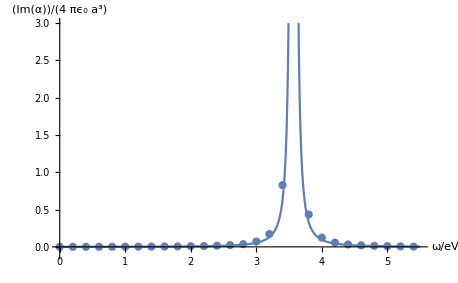

```mathematica
o = 0.005; L = 20;
Show[Show[Plot[Im[α[ω]], {ω, 0, 5.5}, PlotRange->{-0.1, 3}],AxesLabel->{HoldForm[ω/eV],HoldForm[Im[α]/(4 Subscript[πϵ, 0] a^3)]},PlotLabel->None,LabelStyle->{GrayLevel[0]}],
ListPlot[Table[{ω, 1/π N[∫_-L^(ω-o) Re[α[ν]]/(ω - ν)ⅆν + ∫_(ω+o)^L Re[α[ν]]/(ω - ν)ⅆν]}, {ω, 0, 5.5, 0.2}]]]
```

NIntegrate::ncvb: 在接近 {ν} = {-3.52461} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.57077+0. ⅈ 和 0.00609507.

NIntegrate::ncvb: 在接近 {ν} = {3.57264} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.57077+0. ⅈ 和 0.00609507.

NIntegrate::ncvb: 在接近 {ν} = {-3.56317} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.44695+0. ⅈ 和 0.0054381.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

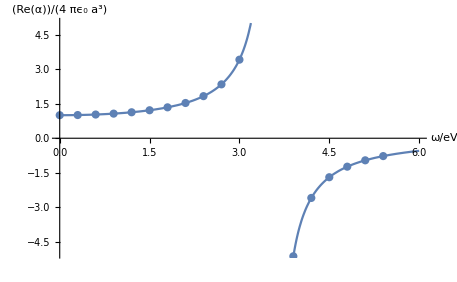

```mathematica
o = 0.01; L = 25;
Show[Show[Plot[Re[α[ω]], {ω, 0, 6}, PlotRange->{-5, 5}],AxesLabel->{HoldForm[ω/eV],HoldForm[Re[α]/(4 Subscript[πϵ, 0] a^3)]},PlotLabel->None,LabelStyle->{GrayLevel[0]}],
ListPlot[Table[{ω,- 1/π N[∫_-L^(ω-o) Im[α[ν]]/(ω - ν)ⅆν + ∫_(ω+o)^L Im[α[ν]]/(ω - ν)ⅆν]}, {ω, 0, 5.5, 0.3}]]]
```